```mathematica
Rz[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}
Rx[a_]:={{1,0,0},{0,Cos[a],-Sin[a]},{0,Sin[a],Cos[a]}}
Ry[a_]:={{Cos[a],0,Sin[a]},{0,1,0},{-Sin[a],0,Cos[a]}}
```

```mathematica
rp[τ_]:={Sin[ω]Cos[τ],Sin[ω]Sin[τ],Cos[ω]}
```

```mathematica
r[τ_]:=Rz[-λ].Ry[π/2-θ].rp[τ]
```

```mathematica
λ=RandomReal[{0,2π}]
θ=RandomReal[{-π/2,π/2}]
ω=.2
```

```mathematica
4.685234349301739
```

```mathematica
1.2157710089276614
```

0.2

```mathematica
gp={Cos[θ]Cos[λ],-Cos[θ]Sin[λ],Sin[θ]}
```

{-0.00943817,0.347486,0.937638}

```mathematica
Show[
Graphics3D[Sphere[{0,0,0}],AxesLabel->{"x","y","z"}],Graphics3D[{PointSize[.05],Red,Point[gp]}],ParametricPlot3D[r[t],{t,0,2π}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-

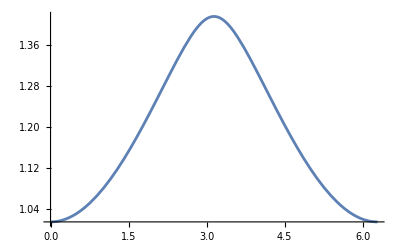

```mathematica
Plot[ArcSin[r[t][[3]]],{t,0,2π}]
```